## §4. Интеграл от функции комплексной переменной.

### 4.1. Интеграл по кривой и его вычисление.

Пусть l - дуга направленной кусочно гладкой кривой в плоскости (z), точки z_k∈l , k=1...n разбивают дугу L на частинчные дуги, на каждой из которых выбрано по одной точке ξ_k. По определению полагаем:

∫_l f(z)ⅆz=lim_(max |Δz_k|→0) ∑_(k=1)^n f(ξ_k)Δz_k

при условии, что предел в правой части (1) существует и не зависит ни от способа разбиения дуги L на частичные дуги, ни от выбора точек ξ_k. Если функция f(z) непрерывна на L, то интеграл (1) существует.

Если f(z)=u(x,y)+ⅈ v(x,y), то вычисление интеграла (1) сводится к вычислению двух интегралов 2-го рода:

∫_l f(z)ⅆz=∫_l u(x,y)d x-v(x,y)d y+ i∫_l v(x,y)d x+u(x,y)d y

##### Пример №11.232

Вычислить интеграл по заданному контору:

∫_l (i z^2-2 z^-)ⅆz, l={z| |z|=2, 0≤ arg z ≤ π/2}

Выделим действительную и мнимую части функции:

```mathematica
f[z_]:=I z^2-2Conjugate[z]
```

Функция Refine преобразовывает выражение при условии, что элементы х и у принадлежат множеству действительных чисел:

```mathematica
u[x_,y_]:=Refine[Re[ComplexExpand[f[x+I y]]],Element[x|y,Reals]]
v[x_,y_]:=Refine[Im[ComplexExpand[f[x+I y]]],Element[x|y,Reals]]
```

Выведем полученные функции:

```mathematica
u[x,y]
v[x,y]
```

-2 x-2 x y

x^2+2 y-y^2

Теперь изобразим контур интегрирования:

```mathematica
With[{z=2 Exp[I phi]},ParametricPlot[ReIm[z],{phi,0,Pi/2},AxesLabel->{Re,Im},PlotRange->{{-1,3},{-1,3}} ,Frame->False,Axes->True]]
```

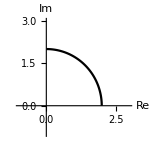

По формуле (2):

∫_l f(z)ⅆz=-∫_0^2 u(x,y)-v(x,y)ⅆy/ⅆx ⅆx-ⅈ∫_0^2 v(x,y)+u(x,y)ⅆy/ⅆx ⅆx

Перед интегралом стоит знак минус, так как обход совершается по часовой стрелке.

Вычислим криволинейный интеграл с помощью замены y=√(4-x^2):

```mathematica
-Integrate[u[x,√(4-x^2)]-v[x,√(4-x^2)] D[√(4-x^2),x],{x,0,2}]-I Integrate[v[x,√(4-x^2)] +u[x,√(4-x^2)]D[√(4-x^2),x],{x,0,2}]
```

8/3-4/3 ⅈ (2+3 π)

Получили ответ:

∫_l (i z^2-2 z^-)ⅆz=8/3-ⅈ (8/3+4 π)

##### Пример №11.241

Вычислить интеграл по заданному контору:

∫_l Im z^2 Re z^3 ⅆz,  l={(x,y)| y=3 x^3,0≤x≤ 1}

Запишем функцию и выделим действительную и мнимую части:

```mathematica
f[z_]:=Im[z^2]Re[z^3]
```

```mathematica
u[x_,y_]:=Refine[Re[ComplexExpand[f[x+I y]]],Element[x|y,Reals]]
v[x_,y_]:=Refine[Im[ComplexExpand[f[x+I y]]],Element[x|y,Reals]]
```

```mathematica
u[x,y]
v[x,y]
```

2 x^4 y-6 x^2 y^3

0

Изобразим контур интегрирования:

```mathematica
Plot[3 x^3,{x,0,1},PlotRange->{{-1/2,3/2},{-1/2,3}}]
```

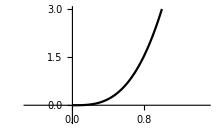

Произведем замену y=3 x^3 и вычислим интеграл по формуле (2):

```mathematica
int=Integrate[u[x,3 x^3]-v[x,3 x^3]D[3 x^3,x],{x,0,1}]+I Integrate[v[x,3 x^3]+u[x,3 x^3]D[3 x^3,x],{x,0,1}]
```

-51/4-(3456 ⅈ)/35

Окончательный ответ:

∫_l Im z^2 Re z^3 ⅆz=-51/4-(3456 ⅈ)/35

Изложенную методику следует применять для того, чтобы решить №№12.230-248, что рекомендуется сделать самостоятельно.

### 4.2. Теорема Коши. Интегральная формула Коши.

Если функция f(z) аналитична в односвязной области D, ограниченной контуром Г, и γ - замкнутый контур в D, то

∮_γ f(z)ⅆz=0

Если функция f(z) непрерывна в замкнутой области то D̄=D∪Г, то справедлива теорема Коши:

∮_Г f(z)ⅆz=0

Если функция f(z) аналитична в многосвязной области D, ограниченной контуром Г и внутренними по отношению к нему контурами γ_1,...,γ_n, и непрерывна в замкнутой области D̄=D∪Γ^+∪(γ^-)_1...∪(γ^-)_n, то:

∮_(Γ^+∪(γ^-)_1...∪(γ^-)_n) f(z)ⅆz=0

Отсюда следует следующая формула:

∮_(Γ^+) f(z)ⅆz=∑_(i=1)^n ∮_(γ_(+_i)) f(z)ⅆz

Если функция f(z) определена и непрерывна в односвязной области D, то если F(z) - одна из первообразных для f(z), то:

∫_z_1^z_2 f(z)ⅆz=F(z_2)-F(z_1)

Если функция f(z) аналитична в односвязной области D, z_0∈D и γ⊂D - замкнутый контур, охватывающий точку z_0, то справедлива интегральная формула Коши

f(z_0)=1/(2π ⅈ)∮_γ (f(z))/(z-z_0)ⅆz

При этом функция f(z) имеет всюду в D производные любого порядка, для которых справедливы формулы:

f^(k)(z_0)=(k!)/(2π ⅈ)∮_γ (f(z))/(z-z_0)^(k+1)ⅆz

##### Пример №12.249

Вычислить интеграл:

∫_l e^z ⅆz, l={(x,y)|y=x^3,1≤ x≤ 2}

Чтобы вычислить интеграл по формуле (6) требуется найти пределы интегрирования. Определим z, как:

```mathematica
z[x_,y_]:=x+I y
```

Тогда точки z_1 и z_2 будут вычисляться следующим образом:

```mathematica
z1=z[x,x^3]/.x-> 1
z2=z[x,x^3]/.x-> 2
```

1+ⅈ

2+8 ⅈ

И тогда интеграл равен:

```mathematica
Integrate[Exp[z],{z,z1,z2}]//ComplexExpand//TrigReduce
```

-ⅇ Cos[1]+ⅇ^2 Cos[8]-ⅈ ⅇ Sin[1]+ⅈ ⅇ^2 Sin[8]

В итоге, получили ответ:

∫_l e^z ⅆz= ⅇ(ⅇ cos(8)-cos(1))+ⅈ ⅇ(ⅇ sin(8)-sin(1))

Данный тип задач не представляет совершенно никакой сложности, поэтому №№12.249-256 рекомендуются к самостоятельному решению.

Рассмотрим следующий тип задач, для решения которых требуется использование интегральной теоремы Коши.

##### Пример №11.258

Вычислить интегралы (обход контуров - против часовой стрелки)

а.  ∮_(|z|=4) ⅇ^(2z)/(z-π ⅈ)ⅆz;           б. ∮_(|z|=1) ⅇ^(2z)/(z-π ⅈ)ⅆz;

Запишем функцию:

```mathematica
f[z_]:=Exp[2z]/(z-I Pi)
```

Из теоремы (8) выразим интеграл:

∮_γ (f(z))/(z-z_0)^(k+1)ⅆz=2π ⅈ (f^(k)(z_0))/(k!)

Изобразим контуры |z|=4 и |z|=1, а также точку z=π ⅈ:

```mathematica
Show[ContourPlot[{x^2+y^2==16,x^2+y^2==1},{x,-4,4},{y,-4,4},Frame->False,Axes->True,AxesLabel->{Re,Im},ImageSize->200,PlotLegends->{"|z|=4","|z|=1"}],Graphics[{PointSize[Large],Point[ReIm[π ⅈ]]}]]
```

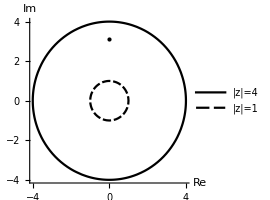

Из графика видно, что:

В случае (б) интеграл равен нулю, так как подынтегральная функция аналитична во всей области |z|≤ 1

В случае (а) точка z=π ⅈ лежит внутри контура интегрирования, следовательно интеграл будет вычисляться по формуле (9):

```mathematica
int=2 Pi I Exp[2z]/.z-> Pi I
```

2 ⅈ π

Получаем ответ:

а.  ∮_(|z|=4) ⅇ^(2z)/(z-π ⅈ)ⅆz=2 ⅈ π;           б. ∮_(|z|=1) ⅇ^(2z)/(z-π ⅈ)ⅆz=0;

##### Пример №11.260

Вычислить интегралы:

а.  ∮_(|z-1|=1) (sin((π z)/2))/(z^2-1)ⅆz;           б. ∮_(|z|=4) (sin((π z)/2))/(z^2-1)ⅆz;

Запишем функцию:

```mathematica
f[z_]:=Sin[Pi z/2]/(z^2-1)
```

Для того чтобы найти значения заданных интегралов, изобразим контуры интегрирования |z-1|=1 и |z|=4, а также точки z_1=1, z_2=-1:

```mathematica
Show[ContourPlot[{(x-1)^2+y^2==1,x^2+y^2==4},{x,-4,4},{y,-4,4},Frame->False,Axes->True,AxesLabel->{Re,Im},ImageSize->200,PlotLegends->{"|z-1|=1","|z|=4"}],Graphics[{PointSize[Large],Point[{{1,0},{-1,0}}]}]]
```

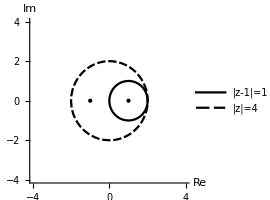

Из графика заключаем что:

В случае (а) внутри контура интегрирования находится одна точка z_1=1, поэтому по формуле (9):

```mathematica
int1=2 I Pi Sin[Pi z/2]/(z+1)/.z->1
```

ⅈ π

В случае (б) внутри контура находятся обе точки z_1=1, z_2=-1, следовательно по теореме о многосвязной области (5) имеем:

∮_(|z|=4) (sin((π z)/2))/(z^2-1)ⅆz=∮_(|z-1|=r) ((sin((π z)/2))/(z+1))/(z-1)ⅆz+∮_(|z+1|=r) ((sin((π z)/2))/(z-1))/(z+1)ⅆz,  где r<2

По Формуле (9):

```mathematica
int2=2I Pi((Sin[Pi z/2]/(z+1)/.z-> 1)+(Sin[Pi z/2]/(z-1)/.z->-1))
```

2 ⅈ π

Итак ответ:

а.  ∮_(|z-1|=1) (sin((π z)/2))/(z^2-1)ⅆz=ⅈ π;           б. ∮_(|z|=4) (sin((π z)/2))/(z^2-1)ⅆz=2 ⅈ π;

##### Пример №11.265

Вычислить интеграл:

∮_(|z-1|=1) ⅆz/((z-1)^3(z+1)^3)

Запишем всё подынтегральное выражение:

```mathematica
f[z_]:=1/((z-1)^3(z+1)^3)
```

На этот раз решим задачу аналитически. Имеется функция f(z) и контур |z-1|=1, требуется найти интеграл.

Первое, что требуется сделать, - это найти точки, в которых функция f(z) теряет аналитичность. Для этого воспользуемся опцией Denominator[ exrp ] , которая возвращает знаменатель выражения expr, причем нас интересуют лишь те точки, которые лежат внутри контура интегрирования:

```mathematica
sol=z/.Solve[Abs[z-1]< 1&&Denominator[f[z]]==0,z]
```

{1,1,1}

Конечно, в данном случае нет ничего сложного, но будем действовать поэтапно: определим кратность каждого из корней (т.к. в формуле (9) нам требуется знать порядок производной). Для этого поступим так:

Рассмотрим уравнение: (z-1)^3(z+1)^3==0

Решая его относительно z, получаем ответ:

```mathematica
solp=z/.Solve[(z-1)^3(z+1)^3==0,z]
```

{-1,-1,-1,1,1,1}

Здесь число повторений корня равно его кратности. Определим сколько раз встречается i-ый элемент при помощи функции Counts:

```mathematica
rule=Counts[solp]
```

<|-1→3,1→3|>

Мы получили ассоциацию вида: <|..., i-ый корень → его кратность,...|>

Теперь, чтобы получить кратность корня, воспользуемся следующей конструкцией:

```mathematica
solp[[1]]/.rule
```

3

В данной конструкции происходит замена корня (z=1) на его кратность (3).

Вернемся к исходной задаче и составим правило замены корня на его кратность:

```mathematica
rule=Counts[sol]
```

<|1→3|>

Теперь определим функцию кратности от порядкового номера корня:

```mathematica
k[i_]:=DeleteDuplicates[sol][[i]]/.Counts[sol]
```

```mathematica
k[1]
```

3

Введем множество уникальных корней (без повторов) при помощи функции DeleteDuplicates:

```mathematica
sol1=DeleteDuplicates[sol]
```

{1}

Теперь, для того чтобы вычислить интеграл, нужно лишь воспользоваться формулами (9) и (5) :

```mathematica
int=2 Pi I  Sum[ (D[ Simplify[ f[z] (z-sol1[[i]])^k[i]],{z,k[i]-1}]/(k[i]-1)!)/.z-> sol1[[i]],{i,1,Length[sol1]}]
```

(3 ⅈ π)/8

Получили ответ:

∮_(|z-1|=1) ⅆz/((z-1)^3(z+1)^3)=(3 ⅈ π)/8

Данную методику следует применять для решения подобных задач, представленных в №№11.257-11.271.

##### Общий алгоритм

При помощи опыта, полученного после решения задачи №11.265, напишем программу, которая будет искать значения контурных интегралов на основе интегральных теорем Коши:

Пусть имеется функция f(z), имеющая вид:

f(z)=(ψ(z))/((z-z_1)^k_1....(z-z_n)^k_n)

Требуется найти интеграл:

∮_C f(z)ⅆz;  C={z| |z-a|=b} , где a и b - параметры

Для решения данной задачи составим алгоритм:

1. Нахождение точек z_1... z_n лежащих внутри |z-a|=b

2. Определение кратности каждой ( k_i)

3. Комбинация формул (5) и (9).

А теперь напишем программный модуль:

```mathematica
integrateC[z_,expr_,a_,b_]:=
Module[{sol,sol1,k},
sol=z/.Solve[Abs[z-a]<b&&Denominator[Simplify@TrigToExp[expr]]==0,z];
sol1=DeleteDuplicates[sol];
k[i_]:=sol1[[i]]/.Counts[sol];
2 I Pi Sum[ Limit[D[ Simplify[ expr(z-sol1[[i]])^k[i]],{z,k[i]-1}]/(k[i]-1)!,z->sol1[[i]]],{i,1,Length[sol1]}]]
```

Разберем устройство полученного модуля:

1. Сначала решаем уравнения Abs[z-a]<b и  Denominator[f[z]]=0. Это позволит нам отыскать z_1... z_n, которые лежат внутри контура интегрирования. Функция TrigToExp нужна для того, чтобы преобразовать тригонометрические функции в экспоненциальные, так как с ними удобнее работать.

2. Составляем множество уникальных корней sol1.

3. Определяем кратность i-ого уникального корня.

4. Используем формулу (9) и (5) для нахождения значения интеграла.

Продемонстрируем примеры:

##### Пример №12.266

```mathematica
integrateC[z,Sin[z]/(z+I)^3,-I,1]
```

-π Sinh[1]

##### Пример №12.270

```mathematica
integrateC[z,1/z^3 Cos[Pi/(z+1)],0,1/2]
```

ⅈ π^3

##### Пример №

```mathematica
integrateC[z,1/Sin[z],0,4]
```

-2 ⅈ π

Полученную функцию добавим в пользовательскую библиотеку, чтобы использовать в дальнейшем.